DVOJITÁ GEOMETRICKÁ TRANSFORMÁCIA ŠTVORCA

==========================================

POČIATOČNÝ ŠTVOREC:

Vrcholy štvorca ABCD:

(-10 | -9
0 | -9
0 | 1
-10 | 1)

Vlastnosti štvorca:

Obsah: 100

Obvod: 40

PRVÁ TRANSFORMÁCIA: Posun

GEOMETRICKÉ TRANSFORMÁCIE ŠTVORCA - POSUN

========================================

ZADANIE:

Majme štvorec ABCD s vrcholmi:

(-10 | -9
0 | -9
0 | 1
-10 | 1)

Vykonajte posun štvorca v 2D priestore pomocou vektora posunu: Δ = [5, -5]

Transformačná matica posunu v homogénnych súradniciach:

(1 | 0 | 5
0 | 1 | -5
0 | 0 | 1)

POSTUP:

Pre výpočet použijeme maticu posunu v homogénnych súradniciach:

Transformačná matica:

(1 | 0 | dx
0 | 1 | dy
0 | 0 | 1)

Pre naše hodnoty:

dx = 5

dy = -5

Posun vykonáme pomocou vzorcov:

x' = x + dx

y' = y + dy

Výpočet pre jednotlivé vrcholy:

Vrchol A:

Pôvodné súradnice: [-10, -9]

Výpočet x-ovej súradnice:

x' = x + dx = -10 + 5

x' = -5

Výpočet y-ovej súradnice:

y' = y + dy = -9 + -5

y' = -14

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -5 + (-5) = -10

y = y' + (-dy) = -14 + (5) = -9

Maticový zápis:

(1 | 0 | 5
0 | 1 | -5
0 | 0 | 1) · (-10
-9
1) = (-5
-14
1)

Vrchol B:

Pôvodné súradnice: [0, -9]

Výpočet x-ovej súradnice:

x' = x + dx = 0 + 5

x' = 5

Výpočet y-ovej súradnice:

y' = y + dy = -9 + -5

y' = -14

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = 5 + (-5) = 0

y = y' + (-dy) = -14 + (5) = -9

Maticový zápis:

(1 | 0 | 5
0 | 1 | -5
0 | 0 | 1) · (0
-9
1) = (5
-14
1)

Vrchol C:

Pôvodné súradnice: [0, 1]

Výpočet x-ovej súradnice:

x' = x + dx = 0 + 5

x' = 5

Výpočet y-ovej súradnice:

y' = y + dy = 1 + -5

y' = -4

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = 5 + (-5) = 0

y = y' + (-dy) = -4 + (5) = 1

Maticový zápis:

(1 | 0 | 5
0 | 1 | -5
0 | 0 | 1) · (0
1
1) = (5
-4
1)

Vrchol D:

Pôvodné súradnice: [-10, 1]

Výpočet x-ovej súradnice:

x' = x + dx = -10 + 5

x' = -5

Výpočet y-ovej súradnice:

y' = y + dy = 1 + -5

y' = -4

Overenie pomocou inverznej transformácie:

x = x' + (-dx) = -5 + (-5) = -10

y = y' + (-dy) = -4 + (5) = 1

Maticový zápis:

(1 | 0 | 5
0 | 1 | -5
0 | 0 | 1) · (-10
1
1) = (-5
-4
1)

VÝSLEDOK:

Vrcholy štvorca po posune:

(-5 | -14
5 | -14
5 | -4
-5 | -4)

VIZUALIZÁCIA:

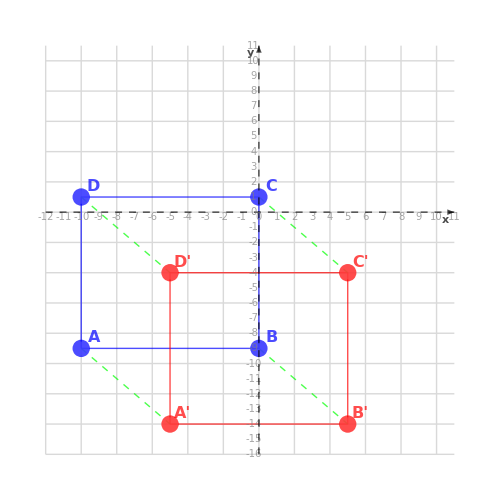

LEGENDA:

• Modré body a čiary: Pôvodný štvorec

• Červené body a čiary: Posunutý štvorec

• Zelená šípka: Vektor posunu

• Zelené prerušované čiary: Posun jednotlivých vrcholov

• Mriežka: Súradnicový systém

Pôvodné vrcholy (modrá):

Vrchol A: {-10,-9}

Vrchol B: {0,-9}

Vrchol C: {0,1}

Vrchol D: {-10,1}

Výsledné vrcholy (červená):

Vrchol A': {-5,-14}

Vrchol B': {5,-14}

Vrchol C': {5,-4}

Vrchol D': {-5,-4}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite vektor posunu:

Δ' = [-5, 5] (opačný vektor)

DRUHÁ TRANSFORMÁCIA: Rotácia

GEOMETRICKÉ TRANSFORMÁCIE ŠTVORCA - ROTÁCIA

========================================

ZADANIE:

Majme štvorec ABCD s vrcholmi:

(-5 | -14
5 | -14
5 | -4
-5 | -4)

Vykonajte rotáciu štvorca v 2D priestore okolo počiatku súradnicovej sústavy [0,0] o uhol α = 60°.

Transformačná matica rotácie:

(1/2 | -(√3)/2
(√3)/2 | 1/2)

POSTUP:

Pre výpočet použijeme maticu rotácie:

Transformačná matica rotácie:

(cos(α) | -sin(α)
sin(α) | cos(α))

Naša hodnota α = 60°:

cos(α) = 1/2

sin(α) = √3/2

Rotáciu vykonáme pomocou vzorcov:

x' = x · cos(α) - y · sin(α)

y' = x · sin(α) + y · cos(α)

Výpočet pre jednotlivé vrcholy:

Vrchol A:

Pôvodné súradnice: [-5, -14]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -5 · 1/2 - -14 · √3/2

x' = -5/2 + 7 · √3

x' = -5/2 + 7 · √3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -5 · √3/2 + -14 · 1/2

y' = -7 - (5 · √3)/2

y' = -7 - (5 · √3)/2

Výsledné súradnice: [-5/2 + 7 · √3, -7 - (5 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = -5/2 + 7 · √3 · 1/2 - -7 - (5 · √3)/2 · -1/2 · √3

x = -5

x = -5 = -5

y = x' · sin(α') + y' · cos(α')

y = -5/2 + 7 · √3 · -1/2 · √3 + -7 - (5 · √3)/2 · 1/2

y = -14

y = -14 = -14

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (-5
-14) = (-5/2+7 √3
-7-(5 √3)/2)

Vrchol B:

Pôvodné súradnice: [5, -14]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = 5 · 1/2 - -14 · √3/2

x' = 5/2 + 7 · √3

x' = 5/2 + 7 · √3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = 5 · √3/2 + -14 · 1/2

y' = -7 + (5 · √3)/2

y' = -7 + (5 · √3)/2

Výsledné súradnice: [5/2 + 7 · √3, -7 + (5 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = 5/2 + 7 · √3 · 1/2 - -7 + (5 · √3)/2 · -1/2 · √3

x = 5

x = 5 = 5

y = x' · sin(α') + y' · cos(α')

y = 5/2 + 7 · √3 · -1/2 · √3 + -7 + (5 · √3)/2 · 1/2

y = -14

y = -14 = -14

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (5
-14) = (5/2+7 √3
-7+(5 √3)/2)

Vrchol C:

Pôvodné súradnice: [5, -4]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = 5 · 1/2 - -4 · √3/2

x' = 5/2 + 2 · √3

x' = 5/2 + 2 · √3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = 5 · √3/2 + -4 · 1/2

y' = -2 + (5 · √3)/2

y' = -2 + (5 · √3)/2

Výsledné súradnice: [5/2 + 2 · √3, -2 + (5 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = 5/2 + 2 · √3 · 1/2 - -2 + (5 · √3)/2 · -1/2 · √3

x = 5

x = 5 = 5

y = x' · sin(α') + y' · cos(α')

y = 5/2 + 2 · √3 · -1/2 · √3 + -2 + (5 · √3)/2 · 1/2

y = -4

y = -4 = -4

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (5
-4) = (5/2+2 √3
-2+(5 √3)/2)

Vrchol D:

Pôvodné súradnice: [-5, -4]

Výpočet x-ovej súradnice:

x' = x · cos(α) - y · sin(α)

x' = -5 · 1/2 - -4 · √3/2

x' = -5/2 + 2 · √3

x' = -5/2 + 2 · √3

Výpočet y-ovej súradnice:

y' = x · sin(α) + y · cos(α)

y' = -5 · √3/2 + -4 · 1/2

y' = -2 - (5 · √3)/2

y' = -2 - (5 · √3)/2

Výsledné súradnice: [-5/2 + 2 · √3, -2 - (5 · √3)/2]

Overenie pomocou inverznej transformácie:

Pre inverzný uhol α' = -60°:

cos(α') = 1/2

sin(α') = -1/2 · √3

x = x' · cos(α') - y' · sin(α')

x = -5/2 + 2 · √3 · 1/2 - -2 - (5 · √3)/2 · -1/2 · √3

x = -5

x = -5 = -5

y = x' · sin(α') + y' · cos(α')

y = -5/2 + 2 · √3 · -1/2 · √3 + -2 - (5 · √3)/2 · 1/2

y = -4

y = -4 = -4

Maticový zápis:

(1/2 | -(√3)/2
(√3)/2 | 1/2) · (-5
-4) = (-5/2+2 √3
-2-(5 √3)/2)

VÝSLEDOK:

Vrcholy štvorca po rotácii:

(-5/2+7 √3 | -7-(5 √3)/2
5/2+7 √3 | -7+(5 √3)/2
5/2+2 √3 | -2+(5 √3)/2
-5/2+2 √3 | -2-(5 √3)/2)

VIZUALIZÁCIA:

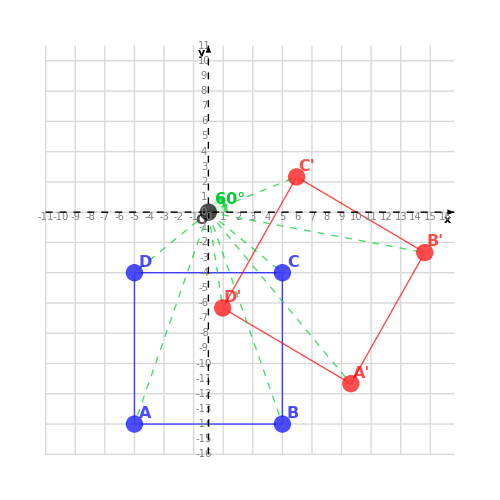

LEGENDA:

• Modré body a čiary: Pôvodný štvorec

• Červené body a čiary: Otočený štvorec

• Zelený oblúk: Znázornenie uhlu rotácie

• Zelené prerušované čiary: Spojenia vrcholov s počiatkom

• Mriežka: Súradnicový systém

• O: Počiatok súradnicovej sústavy - stred rotácie

Pôvodné vrcholy (modrá):

Vrchol A: {-5,-14}

Vrchol B: {5,-14}

Vrchol C: {5,-4}

Vrchol D: {-5,-4}

Výsledné vrcholy (červená):

Vrchol A': {-5/2+7 √3,-7-(5 √3)/2}

Vrchol B': {5/2+7 √3,-7+(5 √3)/2}

Vrchol C': {5/2+2 √3,-2+(5 √3)/2}

Vrchol D': {-5/2+2 √3,-2-(5 √3)/2}

Inverzná transformácia:

Pre vrátenie do pôvodného stavu použite rotáciu o opačný uhol:

α' = -α = -60°

MATEMATICKÉ VLASTNOSTI:

• Rotácia okolo počiatku zachováva vzdialenosť všetkých bodov od počiatku sústavy [0,0]

• Rotácia nemení veľkosť ani tvar geometrických útvarov - je to izometria

• Rotácia zachováva uhly medzi úsečkami a ich dĺžky

• Rotácia zachováva obsah a obvod štvorca

• Počiatok súradnicovej sústavy [0,0] je fixný bod rotácie - zostáva nezmenený

POSTUPNÝ VÝPOČET:

Pôvodný štvorec ABCD:

Vrcholy:

(-10 | -9
0 | -9
0 | 1
-10 | 1)

Vlastnosti štvorca:

Obsah: 100

Obvod: 40

Po prvej transformácii (Posun):

Vrcholy štvorca A'B'C'D':

(-5 | -14
5 | -14
5 | -4
-5 | -4)

Vlastnosti štvorca:

Obsah: 100

Obvod: 40

Po druhej transformácii (Rotácia):

Vrcholy štvorca A''B''C''D'':

(-5/2+7 √3 | -7-(5 √3)/2
5/2+7 √3 | -7+(5 √3)/2
5/2+2 √3 | -2+(5 √3)/2
-5/2+2 √3 | -2-(5 √3)/2)

Vlastnosti štvorca:

Obsah: 100

Obvod: 40

SÚHRNNÁ VIZUALIZÁCIA:

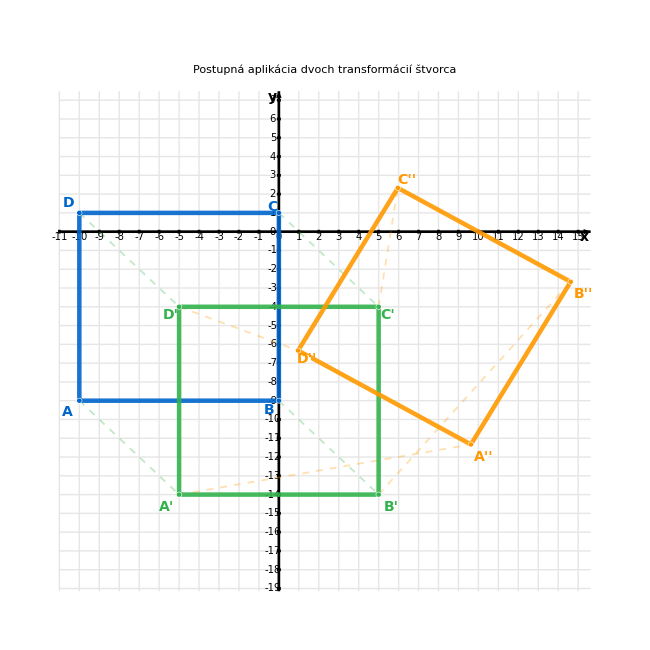

LEGENDA:

• Modré body a čiary: Pôvodný štvorec ABCD

• Tmavozelené body a čiary: Štvorec A'B'C'D' po prvej transformácii (Posun)

• Oranžové body a čiary: Štvorec A''B''C''D'' po druhej transformácii (Rotácia)

Postupnosť transformácií:

1. Posun

2. Rotácia

{{{-10,-9},{0,-9},{0,1},{-10,1}},{{-5,-14},{5,-14},{5,-4},{-5,-4}},{{-5/2+7 √3,-7-(5 √3)/2},{5/2+7 √3,-7+(5 √3)/2},{5/2+2 √3,-2+(5 √3)/2},{-5/2+2 √3,-2-(5 √3)/2}},Posun,Rotácia}

```mathematica
StvorecDvojitaTransformacia[]
```